This the analytical solution to the differential equation:

```mathematica
a=3.5; m=2; τ=1;
f[η_]:= η^(1/m)(((m-1)/(2 m (m+1))) (a^((m+1)/m)-η^((m+1)/m)))^(1/(m-1))
```

```mathematica
u1[x_,t_]:= Piecewise[{{(t+τ)^(-1/m) f[x (t+τ)^(-1/(2 m))],0≤ x ≤ a(t+τ)^(1/(2m))},
{0,a(t+τ)^(1/(2m))< x < ∞  }}]
```

```mathematica
u1[0,0]
```

0.

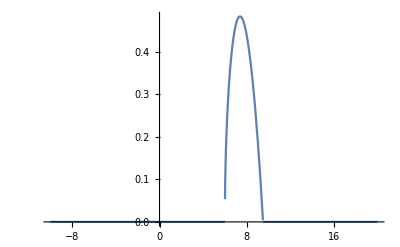

```mathematica
Plot[u1[x-6,0], {x,-10,20}, PlotRange->Full]
```

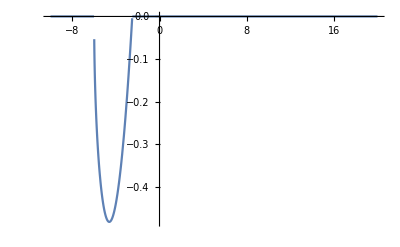

```mathematica
Plot[-u1[6+x,0],{x,-10,20}, PlotRange->Full]
```

```mathematica
abs[x_] := Sqrt[x^2 + 10^-6];
```

```mathematica
Plot[abs[x],{x,-1,1}]
```

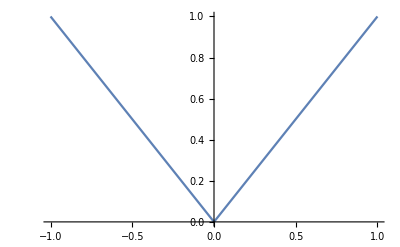

```mathematica
Clear[derabs,x];
```

```mathematica
derabs:= D[abs[x],x]
```

```mathematica
D[abs[x],x]
```

x/(√(1/1000000+x^2))

```mathematica
dabs[x_]:= x/Sqrt[x^2+10^-4]
```

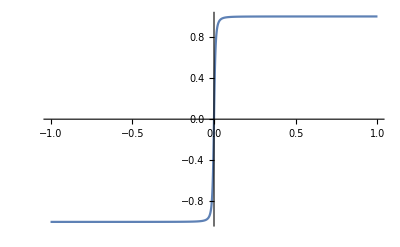

```mathematica
Plot[dabs[x],{x,-1,1}]
```

Seems that Mathematica cant solve equation of type:    ∇^2 (u |u|)=u_t

```mathematica
Clear[u]
ndsol=NDSolveValue[{D[u[t,x],t]==D[u[t,x]*Sqrt[u[t,x]^2+10^-4],x,x],u[0.0,x]==u1[x,0],u[t,20]==u1[20,t],u[t,0]==u1[0,t]},u,{x,0,20},{t,0.01,8.94},MaxStepSize->10^-3]
```

NDSolveValue::eerri: Warning: estimated initial error on the specified spatial grid in the direction of independent variable x exceeds prescribed error tolerance.

InterpolatingFunction[{{0.01, 8.94}, {0., 20.}}, <>]

```mathematica
num=Plot3D[ndsol[t,x], {t,0.01,8.94},{x,0,20},PlotRange->Full,AxesLabel->Automatic]
```

-Graphics3D-

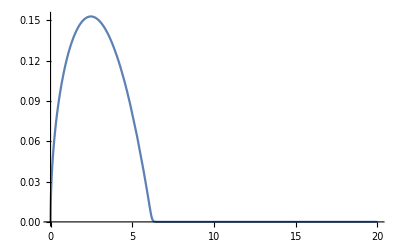

```mathematica
num1=Plot[ndsol[8.93,x], {x,0,20},PlotRange->Full]
```

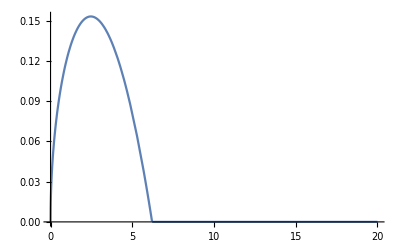

```mathematica
ana=Plot[u1[x,8.93],{x,0,20}]
```

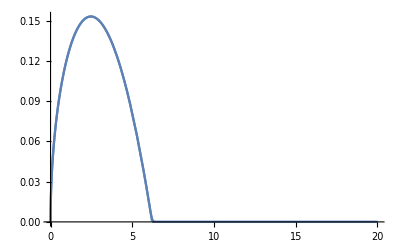

```mathematica
Show[{ana,num1}]
```